## BigSur Package

### External Packages to load

BoolEval is very simple code from Szabolcs Horvát and is available at https : // github . com/szhorvat/BoolEval

```mathematica
<<BoolEval`
```

IGraphM is a paclet from Szabolcs Horvát, available at http://szhorvat.net/ which extends the functionality of IGraph to Mathematica.  You only need to load this if you are going to use the “Find Communities” option of BigSur

```mathematica
<<IGraphM`
```

IGraph/M 0.6.2 (July 25, 2022)
Evaluate IGDocumentation[] to get started.

### What is a Matpac?

The matpac is just BigSur’s data structure for storing scRNAseq counts data.  It is a list with four elements.  The first element is a matrix where the rows correspond to genes and the columns correspond to cells and the entries are UMIs.  The second element is the list of gene names or IDs corresponding to the rows of the matrix.  The third element is a list of cell IDs corresponding to the columns of the matrix.  The fourth element is a list of metadata.

### Manipulation of lists and matrices (Width, SymmetricMatrixToList, RestoreSymmetryExceptDiagonal, ListIndex, MatrixIndexCF, DotProductCF)

#### Width

```mathematica
Width[mat_]:= Last[Dimensions[mat]]
```

#### SymmetricMatrixToList

There are times when it is inconvenient to store a symmetric matrix as a matrix, and easier to store it as a flat list, for example when they have been strictly lower-triangularized (i.e. zeros on the diagonal and in the upper triangle).  The following code replaces a symmetric matrix with the values of the Array Rules that would result from the strictly lower-triangularized version of the matrix.  Note that there should be Binomial[m,2] values, where m- is the common dimension or the original matrix

```mathematica
SymmetricMatrixToList[matrix_]:=Values[Drop[ArrayRules[SparseArray[LowerTriangularize[matrix, -1]]],-1]]
```

#### RestoreSymmetryExceptDiagonal

This takes a symmetric matrix that has been “lower-triangularized” and had its diagonal entries set to zero, and undoes these steps, restoring symmetry to the matrix and not affecting the diagonal.  The output is in the form of a normal array or sparse array, depending on the input

```mathematica
RestoreSymmetryExceptDiagonal[mat_]:= mat+Transpose[mat]
```

#### ListIndex

This code takes any row-column coordinates from a strictly lower triangularized matrix and returns its position in the list generated by SymmetricMatrixToList

```mathematica
ListIndex[{x_, y_}]:=1/2 (2-3 x+x^2+2 y)
```

#### MatrixIndexCF

This compiled code takes any list coordinate from a list that had been generated by SymmetricMatrixToList and returns the row-column coordinates in the corresponding strictly lower triangularized matrix.

```mathematica
MatrixIndexCF= Compile[{{z, _Integer}},With[{x= IntegerPart[1/2 (3+√(-7+8 z))]}, {x, 1/2 (-2+3 x-x^2+2 z)}], RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

#### DotProductCF

DotProductCF is a compiled version of taking a DotProduct.  It operates on a matrix, and generates a matrix of Absolute Correlations multiplied by the vector length, which comes out to simply be the dot product of each vector with each other vector.   If this is applied to a matrix that has been unitized, then the entries represent a count of the numbers of positions where both vectors had a non-zero entry.

```mathematica
DotProductCF=Compile[{{mat, _Real, 2},{n, _Integer}},
n*AbsoluteCorrelation[Transpose[mat]], RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

### Finding Modules in Graphs (FindCommunities)

#### FindCommunities

The function IGCommunitiesWalktrap does the work of implementing the walktrap algorithm of Pons and Latapy*, but needs to take an AdjacencyGraph as in input, which in this case is obtained from the output of a gNetworkObject.    In this function there’s an option, “Steps”, which allows one to set the number of steps used by IGCommunitiesWalkTrap.  The default is 4.  The output is a list of lists of gene communities.  For large, very highly interconnected graphs this can take a long time, so there is a Timeout parameter that can be adjusted, which is set for a default of 5 minutes.
	*Pons P, Latapy M (2005) Computing communities in large networks using random walks . Computer and Information Sciences - Iscis 2005, Proceedings 3733 : 284 - 293

```mathematica
Options[FindCommunities]={"Steps"-> 4, "Timeout"-> 300};FindCommunities[gNetObj_, OptionsPattern[]]:=TimeConstrained[gNetObj⟦2,#⟧&/@IGCommunitiesWalktrap[AdjacencyGraph[gNetObj⟦1⟧], OptionValue["Steps"]]["Communities"],
OptionValue["Timeout"],Print["Timed out"]]
```

### Statistical Analysis (BenjaminiHochberg, BHNew, FixedPvalFunc)

#### BH and BHNew (BenjaminiHochberg)

This code implements the Benjamini Hochberg procedure for correcting multiple sampling by finding a cutoff p-value below which a certain FDR is achieved.  In this procedure, one orders a set of p-values and sequentially queries, from lowest to highest, whether a p-value is less than its rank times the stipulated FDR divided by the total number of p-values.  It returns the first p-value for which this condition fails.  That may be used as a cutoff p-value, below which statistical significance is achieved.  

N.B. if we are using this on a list where a whole bunch of p-values exist but are not being explicitly stored because they are known to be below some threshold, we need to account for that.  So the second version of the function adds the argument, altlength, where we specify a different length to use as the true number of p-values.  

The second version of these functions uses a compiled intermediate function to speed up the running time four to five fold

```mathematica
BH[pvals_, α_]:=
Module[{list= Sort[pvals]},
list[[First[FirstPosition[(list*Length[pvals])/Range[Length[list]], x_/;x>α]]]]]
```

```mathematica
BH[pvals_, α_, altlength_]:=
Module[{list= Sort[pvals]},
list[[First[FirstPosition[(list* altlength)/Range[Length[list]], x_/;x>α]]]]]
```

```mathematica
BHCF=
Compile[{{sortedpvals, _Real, 1}, {altlength, _Integer}},
(sortedpvals* altlength)/Range[Length[sortedpvals]],RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
BHNew[pvals_, α_]:=
Module[{list=Sort[pvals]},
list⟦
Min[Length[list],
1+LengthWhile[BHCF[list, Length[list]], #≤ α&]]
⟧]
```

```mathematica
BHNew[pvals_, α_, altlength_]:=
Module[{list=Sort[pvals]},
list⟦
Min[Length[list],
1+LengthWhile[BHCF[list, altlength], #≤ α&]]
⟧]
```

#### FixedPValFunc

To obtain a -Log10(p)-value from Cornish Fisher Polynomials, we solve for the root of the polynomial, and then feed the result into either -Log10[1/2 Erfc[ -x/(√2)]] or -Log10[1-1/2 Erfc[ -x/(√2)]] depending on whether the observed modified corrected correlation coefficient is negative, or positive, respectively.  

Note that we can rewrite -Log10[1/2 Erfc[ -x/(√2)]] as -Log10[ 1/2(1-Erf[x/(√2)])] and -Log10[1/2 (1-Erf[-x/(√2)]), respectively.  In fact if we are absolutely certain that all the roots of the polynomials corresponding to negative correlations are negative, we could even write a single function:  -Log10[ 1/2(1-Erf[Abs[x]/(√2)])].  
Unfortunately, there are numerical issues with evaluating Erf[x/(√2)] when x >8.3, giving zero instead of the necessary tiny number (at  x=8.3 the pvalue comes out to 1.11022×10^-16, so basically it sets all pvalues lower than 1.11022×10^-16 to 0, which is inconvenient as that makes our Log pvalues Indeterminate.

Fortunately,as  x→∞, it is well known that -Log[1-Erf[z]]→ z^2, thus-Log[1/2(1-Erf[z])] -> z^2+Log[2], thus -Log10[1/2(1-Erf[z])] is just  (z^2+Log[2])/Log[10].  Putting in x/(√2) for z^2 gives us (x^2/2+Log[2])/Log[10]

The following functions therefore replace 1/2(1-Erf[x/(√2)]) with 1/2 e^(-x^2/2),  when x is large, which is an excellent approximation.

Piecewise[{{N[1+(x^2/2+Log[2])/Log[10],4],x>8.3},{N[-Log10[ 1/2(1-Erf[x/(√2)])],4],0<x<= 8.3},{0,True}}];

Since the roots of significant negative correlations are always negative, and roots of positive correlations always positive.  we may use the following compiled function for all cases:

```mathematica
FixedPValFunc=Compile[{{x, _Real}}, If[Abs[x]>8.3,N[1+(x^2/2+Log[2])/Log[10],4],N[-Log10[1/2 (1-Erf[Abs[x]/(√2)])],4]], RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

### BIGSUR (Basic Informatics and Gene Statistics from Unnormalized Reads) (FanoCumulants5CF, CornishFisherPolynomialCoefficientsforFano5CF, InverseSqrtMomentLists, SqrtCorrectionmats, CorrelationCumulantsNewCF, CornishFisherPolynomialCoefficients 5CF, NewFindXAlt, InferredPCCs2, CreateGNO, TruncateGNO, GeneSubsetGNO, FindBestC, BigSur)

#### FanoCumulants5CF

```mathematica
FanoCumulants5CF=
Compile[{{ematrix, _Real, 2},{c,_Real},{n,_Real} },
Module[{χ=1+c^2},
{-1/n+Total/@((1+ematrix (-4+7 χ+6 ematrix (1-2 χ+χ^3)+ematrix^2 (-3+6 χ-4 χ^3+χ^6)))/(ematrix (n+ematrix n (-1+χ))^2)),
Total/@(1/(ematrix^2 (n+ematrix n (-1+χ))^3)(1+ematrix (-9+31 χ)+2 ematrix^2 (16-57 χ+45 χ^3)+ematrix^3 (-56+180 χ-21 χ^2-168 χ^3+65 χ^6)+3 ematrix^4 (16-48 χ+14 χ^2+40 χ^3-6 χ^4-21 χ^6+5 χ^10)+ematrix^5 (-16+48 χ-24 χ^2-30 χ^3+12 χ^4+18 χ^6-3 χ^7-6 χ^10+χ^15))),
Total/@(1/(ematrix^3 (n+ematrix n (-1+χ))^4)(1+ematrix (-15+127 χ)+ematrix^2 (92-674 χ+966 χ^3)+ematrix^3 (-302+1724 χ-271 χ^2-2804 χ^3+1701 χ^6)+6 ematrix^4 (96-452 χ+174 χ^2+620 χ^3-102 χ^4-511 χ^6+175 χ^10)+2 ematrix^5 (-320+1344 χ-822 χ^2-1390 χ^3+672 χ^4+1124 χ^6-151 χ^7-590 χ^10+133 χ^15)+4 ematrix^6 (96-384 χ+312 χ^2+278 χ^3-276 χ^4+18 χ^5-194 χ^6+84 χ^7-9 χ^9+126 χ^10-15 χ^11-43 χ^15+7 χ^21)+ematrix^7 (-96+384 χ-384 χ^2-160 χ^3+314 χ^4-48 χ^5+112 χ^6-120 χ^7+12 χ^8+24 χ^9-80 χ^10+24 χ^11-3 χ^12+32 χ^15-4 χ^16-8 χ^21+χ^28))),
Total/@(1/(ematrix^4 (n+ematrix n (-1+χ))^5)(1+ematrix (-25+511 χ)+30 ematrix^2 (8-119 χ+311 χ^3)+5 ematrix^3 (-248+2540 χ-561 χ^2-7208 χ^3+6821 χ^6)+ematrix^4 (3904-29880 χ+15690 χ^2+68000 χ^3-12990 χ^4-86865 χ^6+42525 χ^10)+ematrix^5 (-7872+49360 χ-39660 χ^2-81110 χ^3+46460 χ^4+98270 χ^6-13365 χ^7-74910 χ^10+22827 χ^15)+20 ematrix^6 (512-2832 χ+2898 χ^2+3168 χ^3-3654 χ^4+216 χ^5-3109 χ^6+1499 χ^7-240 χ^9+2953 χ^10-315 χ^11-1390 χ^15+294 χ^21)+10 ematrix^7 (-832+4288 χ-5136 χ^2-2940 χ^3+6222 χ^4-1008 χ^5+2276 χ^6-2778 χ^7+172 χ^8+806 χ^9-2636 χ^10+842 χ^11-65 χ^12-90 χ^13+1420 χ^15-140 χ^16-476 χ^21+75 χ^28)+5 ematrix^8 (768-3840 χ+5184 χ^2+1152 χ^3-5656 χ^4+1728 χ^5-936 χ^6+2432 χ^7-420 χ^8-960 χ^9+1448 χ^10-912 χ^11+186 χ^12+192 χ^13-720 χ^15+170 χ^16-12 χ^18+288 χ^21-28 χ^22-73 χ^28+9 χ^36)+ematrix^9 (-768+3840 χ-5760 χ^2+320 χ^3+5280 χ^4-2536 χ^5+560 χ^6-2240 χ^7+840 χ^8+980 χ^9-1072 χ^10+880 χ^11-300 χ^12-210 χ^13+400 χ^15-180 χ^16+20 χ^17+40 χ^18-170 χ^21+40 χ^22+50 χ^28-5 χ^29-10 χ^36+χ^45)))}],RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

#### CornishFisherPolynomialCoefficientsforFano5CF

Rather than try to generate the intact polynomials, this code just returns their coefficients as a list of matrices.  The matrices go in order from the coefficients of lowest to highest order, i.e. a+ bx +cx^2+dx^3, etc.

```mathematica
CornishFisherPolynomialCoefficientsforFano5CF=
Compile[{{κ2, _Real, 1}, {κ3, _Real,1},{κ4, _Real,1},{κ5, _Real,1}, {cc, _Real, 1}},
{(1-cc-κ3/(6 κ2)+(17 κ3^3)/(324 κ2^4)-(κ3 κ4)/(12 κ2^3)+κ5/(40 κ2^2)), (√κ2+(5 κ3^2)/(36 κ2^(5/2))-κ4/(8 κ2^(3/2))), (κ3/(6 κ2)-(53 κ3^3)/(324 κ2^4)+(5 κ3 κ4)/(24 κ2^3)-κ5/(20 κ2^2)),  (-κ3^2/(18 κ2^(5/2))+κ4/(24 κ2^(3/2))),(κ3^3/(27 κ2^4)-(κ3 κ4)/(24 κ2^3)+κ5/(120 κ2^2))}, RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

#### InverseSqrtMomentLists

This produces a list of moments 2,3,4 and 5 of 1/√ϕ' for a series of 8 cases of different expectation value.  The reason we don’t need moment 1 is because it will ultimately be multiplied by something with a first moment of zero, so the net moment will be zero regardless.  

The input requires “genetotals”, which is the totals of the URM for each gene, as previously calculated in an early step of BigSur
Likewise depthlist is an early calculation done by BigSur

The output is a series of four lists of datapoints, representing Moments 2, 3, 4 and 5, where the data points are in the form of {“genetotal”, “moment value”}

```mathematica
InverseSqrtFanoMoments[elist_, c_,n_, trials_]:=
{ Moment[#,2],Moment[#,3], Moment[#,4], Moment[#,5]}&@Table[1/√(1/(n-1)Total[((RandomVariate[PoissonDistribution[RandomVariate[LogNormalDistribution[Log[#/(√(1+c^2))],√Log[1+c^2]]]]]-#)^2)/(#(1+c^2#))&/@elist]),trials]
```

```mathematica
InverseSqrtMomentLists[genetotals_,depthlist_, c_, n_]:=
With[{a =Max[2,Min[genetotals]],e=n/50, h= Max[genetotals]},
With[{glist={a,a(e/a)^(1/4),a(e/a)^(1/2),a(e/a)^(3/4),e, e(h/e)^(1/3),e(h/e)^(2/3),h}},
With[{simEmatrix=KroneckerProduct[glist, depthlist]},MapThread[List, {glist, #}]&/@Transpose[Table[InverseSqrtFanoMoments[simEmatrix[[i]], c,n,Round[40000000./(n( Log10[glist[[i]]]^(1/5)+0.5 Log10[glist[[i]]]^3))]], {i, 1, Length[simEmatrix]}]]]]]
```

Note the use of “Max[2,.]” which serve to avoid values of 1, which when logarithms are taken later produce values of infinity for the Table’s iterator.

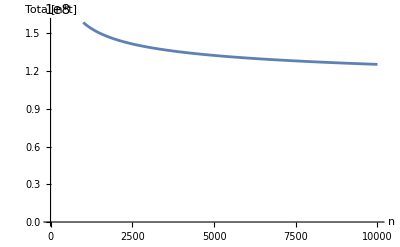

```mathematica
Plot[With[{a=2.,e=n/50, h=2000000.},With[{glist={a,a(e/a)^(1/4),a(e/a)^(1/2),a(e/a)^(3/4),e, e(h/e)^(1/3),e(h/e)^(2/3),h}}, Simplify[Total[Table[18000000/Log10[glist[[i]]], {i, 8}]]]]], {n, 1000, 10000},PlotRange-> {0, Automatic}, AxesLabel-> {"n", "Total[n*t]"}]
```

#### SqrtCorrectionmats

This takes the output of InverseSqrtMomentLists,  and generates four sets of correction matrices for use on the gene pair data.  These square matrices represent moments 2-5 of distributions under the null hypothesis of 1/(√(ϕ_('a)ϕ_('b))) where a and b are the genes.  
Quiet is used to suppress error messages because occasionally the genetotals are below 2 (i.e. just 1 UMI) yet the interpolation function does not go down to datapoints below 2, causing the computer to extrapolate instead.

```mathematica
SqrtCorrectionmats[invsqrtmoments_,genetotals_]:=
Quiet[Module[{
list2 = 10^Interpolation[Log10[invsqrtmoments[[1]]], InterpolationOrder->1][#]&/@Log10[genetotals],
list3 = 10^Interpolation[Log10[invsqrtmoments[[2]]], InterpolationOrder->1][#]&/@Log10[genetotals],
list4 = 10^Interpolation[Log10[invsqrtmoments[[3]]], InterpolationOrder->1][#]&/@Log10[genetotals],
list5 = 10^Interpolation[Log10[invsqrtmoments[[4]]], InterpolationOrder->1][#]&/@Log10[genetotals]},
{KroneckerProduct[list2, list2],KroneckerProduct[list3, list3],KroneckerProduct[list4, list4],KroneckerProduct[list5, list5]}]];
```

#### CorrelationCumulantsNewCF

This code finds the values of cumulants 2,3,4 and 5 .  The matrices ℱ2,  ℱ3, ℱ4, and ℱ5  are the output of InverseSqrtMomentLists.

What it returns is a list of square matrices, starting with κ_2, in the form {κ_2, κ_3, κ_4, κ_5}

```mathematica
CorrelationCumulantsNewCF=
Compile[{{ematrix, _Real, 2},{ℱ2, _Real, 2},{ℱ3, _Real, 2},{ℱ4, _Real, 2},{ℱ5,_Real, 2},{c,_Real},{n,_Real} },
{1/(-1+n)^2 ℱ2 n,
1/(-1+n)^3 ℱ3 DotProductCF[(1+c^2 ematrix (3+c^2 (3+c^2) ematrix))/(√ematrix (1+c^2 ematrix)^(3/2)) , n],
1/(-1+n)^4(-3 n ℱ2^2  + ℱ4 DotProductCF[(1+ematrix (3+c^2 (7+ematrix (6+3 c^2 (6+ematrix)+c^4 (6+(16+15 c^2+6 c^4+c^6) ematrix)))))/(ematrix (1+c^2 ematrix)^2),n] ),

1/(-1+n)^5 (-10 ℱ2 ℱ3 DotProductCF[ (1+c^2 ematrix (3+c^2 (3+c^2) ematrix))/(√ematrix (1+c^2 ematrix)^(3/2)) ,n] +ℱ5 DotProductCF[ 1/(ematrix^(3/2) (1+c^2 ematrix)^(5/2))(1+5 (2+3 c^2) ematrix+5 c^2 (8+15 c^2+5 c^4) ematrix^2+10 c^4 (6+17 c^2+15 c^4+6 c^6+c^8) ematrix^3+c^6 (30+135 c^2+222 c^4+205 c^6+120 c^8+45 c^10+10 c^12+c^14) ematrix^4),n])},RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

#### CornishFisherPolynomialCoefficients 5CF

Rather than try to generate the intact polynomials, this code just returns their coefficients as a list of matrices.  The matrices go in order from the coefficients of lowest to highest order, i.e. a+ bx +cx^2+dx^3, etc.

```mathematica
CornishFisherPolynomialCoefficients5CF=
Compile[{{κ2, _Real, 2}, {κ3, _Real, 2},{κ4, _Real, 2},{κ5, _Real, 2}, {cc, _Real, 2}},
{-cc-κ3/(6 κ2)+(17 κ3^3)/(324 κ2^4)-(κ3 κ4)/(12 κ2^3)+κ5/(40 κ2^2), (√κ2+(5 κ3^2)/(36 κ2^(5/2))-κ4/(8 κ2^(3/2))), (κ3/(6 κ2)-(53 κ3^3)/(324 κ2^4)+(5 κ3 κ4)/(24 κ2^3)-κ5/(20 κ2^2)),(-κ3^2/(18 κ2^(5/2))+κ4/(24 κ2^(3/2))),(κ3^3/(27 κ2^4)-(κ3 κ4)/(24 κ2^3)+κ5/(120 κ2^2))}, RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

#### NewFindXAlt

First we generate some code that NewFindXAlt calls :
Both of them first identify x-boundary values equal to plus or minus √2 InverseErfc[2. 10^-cutoff], which are the x-values corresponding to a particular p-value threshold.

QuickTest6CF returns a zero if the signs at the xboundary values are different, or the sign at x=0 is different from at the positive x-boundary value, and 1 otherwise.  Note that the following function might run faster, provided that ContainsAll can be compiled.

```mathematica
QuickTest6CFAlt=Compile[{{a, _Real},{b, _Real},{c, _Real},{d, _Real},{e, _Real}, {cutoff, _Real}},With[{k=√2 InverseErfc[2. 10^-cutoff]},If[Abs[Total[Table[Sign[a+b x+c x^2+d x^3+e x^4], {x, {-k,- (2k)/3, -k/3, 0, k/3, (2k)/3,k}}]]]==7,1,0]], RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

```mathematica
SecondTestCF=Compile[{{a, _Real},{b, _Real},{c, _Real},{d, _Real},{e, _Real}, {cutoff, _Real}},With[{x=√2 InverseErfc[2. 10^-cutoff]},
Which[
Sign[b-2 c x+3 d x^2-4 e x^3]==-1,1,(*if the slope at -X isn't positive we keep*)
Sign[b+2 c x+3 d x^2+4 e x^3]==-1,0,(*if the slope at X is negative we reject*)
3 d^2<8 c e,1,(*if there is no inflection point we keep*)
-x<(3 d-√(9 d^2-24 c e))/(12 e)<x &&Sign[45 d^3-36 c d e-15 d^2 √(9 d^2-24 c e)+8 e (9 b e-c √(9 d^2-24 c e)) ]==-1,0,(*if the location of the first inflection point is in [-X,X] AND the slope at that point is negative, we reject*)
-x<(3 d+√(9 d^2-24 c e))/(12 e)<x &&  Sign[45 d^3-36 c d e+15 d^2 √(9 d^2-24 c e)+8 e (9 b e+c √(9 d^2-24 c e))]==-1,0,(*otherwise, if the location of the second inflection point is in [-X,X] AND  slope at that point is negative, we reject*)
True,1 (*otherwise we keep*)]],
RuntimeAttributes->{Listable}, Parallelization->True]
```

CompiledFunction[…]

```mathematica
FixedFirst[list_]:= If[Length[list]>0, First[list]];
FixedLast[list_]:= If[Length[list]>0, Last[list]];
```

```mathematica
SmallerInterval[list_]:=
If[
Abs[Last[First[list]]]<Abs[First[Last[list]]],First[list], Last[list]]
```

```mathematica
Foundroots[params_]:=
With[{eqn =params.{1, x, x^2, x^3, x^4,0} },
With[{list= N@First[RootIntervals[eqn]]},
With[{spanningset =Select[list,  Sign[Times[First[#],Last[#]]]==-1&] },
Which[
Length[spanningset]>0, 
x/.FindRoot[eqn, Flatten[{x, spanningset}], Method->"Secant"],
Length[list]==0, 
z, 
Length[list]==1,
x/.FindRoot[eqn, Flatten[{x, list}], Method->"Secant"],
True, 
x/.FindRoot[eqn, Flatten[{x, Flatten@SmallerInterval[{FixedLast@Select[list, Last[#]<0&],FixedFirst@Select[list, First[#]>0&]}/.Null-> Nothing]}], Method-> "Secant"] ]
]]]
```

```mathematica
FindZ[augmentedParams_]:=
With[{rootrules=Select[NSolve[0==augmentedParams.{0,1,2 x,3 x^2,4 x^3,0},x], Im[x/.#]==0&]}, 
With[{vals=Chop[augmentedParams.{1, x, x^2, x^3, x^4,0}/.rootrules]},
x/.rootrules[[First[Ordering[Abs[vals]]]]]]]
```

Here are the steps.

We begin with a list of augmented parameters of length Binomial[m,2].  Let use define -X and X as the X-positions corresponding to our p-value cutoff.  

Step 1:  We apply QuickTest6CF to all the augmented parameters to generate a list of positions called “posns1” where QuickTest6CF returns 1.  The indexing of posns1 runs from 1 to Binomial[m,2].   QuickTest6CF is a fast function that takes as input a list of augmented parameters, and a -logpvalue cutoff, and outputs 1 or 0 to indicate whether the values of the polynomial at x= -X and x=X are different, or whether the values at x= -X and x= X have the same sign, but one that is different from the value at x=0.   If they do then, by continuity we know that there is a root between -X and X, i.e. a root that will produce a -logp-value below the cutoff.   So our first step is to identify all the polynomials that cannot be excluded on these grounds.  

Step 2:  We know that gene pair correlations involving very lowly expressed genes sometimes don’t display an actual root between -X and X, but come close to doing so, and should be excluded from further consideration whenever that happens.  We call that having a “quasiroot”.   Empirically, we find that this happens when the maximum gene expression in the pair is <0.05 (given 1662 cells), i.e. when the total UMI in the most highly expressed gene amounts to less than 84.  So we need to find the positions in our augmented parameters list where there is a quasiroot.  

First we generate a Sparse Matrix of just gene pairs where the maximum gene expression meets that criterion, and then use ListIndex to convert the Explicit Positions to list indices.  We then use that to divide the positions from the previous step into two groups, “posns1high” and “posns1low” for gene expression.  We then take the posns1low and apply SecondTestCF.  This test does a series of things:
	1) If the slope at -X isn’t positive, there isn’t a quasiroot (we find empirically that the slope at -X is always positive, but we check anyway)
	2) Then, if the slope at X is negative it guarantees a maximum between -X and X, which we take to be a quasiroot,
	3) If either of the only possible inflection points (the positions of which can be solved for analytically as (3 d-√(9 d^2-24 c e))/(12 e) and (3 d+√(9 d^2-24 c e))/(12 e) ) lies between -X and X, if the slope at either of them is negative then there must have been a maximum between -X and X.  Note that the slopes at each of these points are (45 d^3-36 c d e-15 d^2 √(9 d^2-24 c e)+8 e (9 b e-c √(9 d^2-24 c e)))/(72 e^2) and (45 d^3-36 c d e+15 d^2 √(9 d^2-24 c e)+8 e (9 b e+c √(9 d^2-24 c e)))/(72 e^2), however in testing their signs we may exclude the 72 e^2 in the denominator because, being a square it is necessarily positive so it has no influence on the sign.  
	
Step 3:  We define posns2 as the union of posns1high and those elements of posns1low that passed the slope and intercept tests.  The indexing of these still runs from 1 to Binomial[m,2]

Step 4:  We apply Foundroots to augmentedParameters[[posns2]].  This finds roots except where no true roots exist in which case it returns z.  
	To those cases where no root was  found, we use FindZ to return a quasi-root.  We then replace the z’s with these quasiroots; the whole thing together is called rootsComplete.  This list has the same length as posns2.  Thus if we want to find out which augmented parameters go with which roots we match them up with augmentedparameters[[posns2]].
	
Step 5:  We use Benjamini Hochberg to find the significance cutoff for FixedPValFunc/@rootsComplete, using Binomial[m,2] as our Array length.   We define checkposns as those locations within rootsComplete where the BH cutoff was exceeded.  In order to get this indexing back to that of augmentedparameters we take posns2[[checkposns]]

Step6:  We now want to search for additional quasiroots, at those check-positions, where the quasiroot falls below the BH cutoff.  We remove any of those as well from the list.  Finally, we index the list by augmentedparameters[[posns2]]

```mathematica
NewFindXAlt[augmentedParameters_,cutoff_, genetotals_, alpha_]:=
Module[{ passedTest,passedTest2,lowposns,posns1low, posns1high,posns2,  trueroots, rootsComplete,logpcriterion, checkposns,additionalQuasirootsPosns, rootsFinal},
(*step 1*)
passedTest=Flatten[SparseArray[QuickTest6CFAlt[#1, #2, #3, #4, #5, cutoff]&@@#&/@augmentedParameters]["ExplicitPositions"]];
Print["First quick test complete.  Surviving parameter sets = ", Length[passedTest], TimeObject[Now]];
(*step 2*)
lowposns=ListIndex/@(SparseArray[LowerTriangularize[KroneckerProduct[SparseArray[BoolEval[genetotals<84]], SparseArray[BoolEval[genetotals<84]]],-1]]["ExplicitPositions"]);
posns1low = Intersection[passedTest, lowposns];
posns1high = Complement[passedTest, lowposns];
passedTest2=SecondTestCF[#1, #2, #3, #4, #5, cutoff]&@@#&/@augmentedParameters[[posns1low]];
(*step3*)
posns2=Union[If[passedTest2=={},{},
posns1low[[Flatten[SparseArray[passedTest2]["ExplicitPositions"]]]]], posns1high];
Print["Second quick test complete.  Surviving parameter sets = ",Length[posns2],TimeObject[Now]];
(*step 4*)
trueroots =  Foundroots/@augmentedParameters[[posns2]];
Print["True roots found",TimeObject[Now]];
rootsComplete=ReplacePart[trueroots, Thread[Flatten[Position[trueroots, z]]-> FindZ/@augmentedParameters[[posns2]][[Flatten[Position[trueroots, z]]]]]];
(*step 5*)
logpcriterion=-Log10@BHNew[10^-(FixedPValFunc/@rootsComplete),alpha,Binomial[Length[genetotals],2] ];
Print["p criterion = ",ScientificForm[10^-logpcriterion],TimeObject[Now]];
checkposns=
Flatten@Position[FixedPValFunc/@rootsComplete, x_/;x> logpcriterion];
additionalQuasirootsPosns=posns2[[checkposns[[Flatten[Position[FixedPValFunc/@(FindZ/@augmentedParameters[[posns2[[checkposns]]]]), x_/;x<logpcriterion]]]]]];
rootsFinal=ReplacePart[rootsComplete,additionalQuasirootsPosns-> 0];
SparseArray[Thread[posns2-> rootsFinal], Length[augmentedParameters]]
]
```

#### InferredPCCs2

This operates on a matrix of log-transformed pvalues,  and on a matrix containing the signs of PCC’.  It produces a matrix equivalent correlation coefficients.  It calls a code that uses the Fisher p-value formula to give an equivalent correlation coefficient based on the p-value and the vector length.  

Because it is relatively slow, it first prunes the pvalue matrix to set any values less than or equal to “cutoff” to zero.

```mathematica
InferredPCCs2[logpvalmatrix_,pccSignmatrix_, cutoff_, n_]:= 
Module[{mat=SparseArray[logpvalmatrix*BoolEval[logpvalmatrix>cutoff],Dimensions[logpvalmatrix]], sa,be, mat2, sa2},
sa=SparseArray[pccSignmatrix *Tanh[(√2 InverseErfc[ 10^-mat])/(√(-3.+n))], Dimensions[mat]];
be=BoolEval[Abs[sa]==1];
mat2 = SparseArray[logpvalmatrix*be];
sa2 =SparseArray[pccSignmatrix *Tanh[ (√(2 Log[ 10]))/(√(-3.+n))√mat2]] ;
sa+sa2-sa*be]
```

Note that for really low p-values the formula Tanh[(√2 InverseErfc[ 10^-#])/(√(-3.+n))] will fail for numerical reasons and return 1.  In those cases we use Tanh[(√(2 Log[ 10]))/(√(-3.+n))√#] instead.

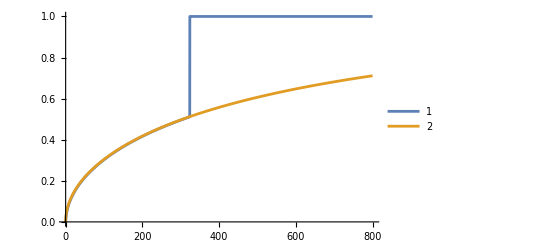

```mathematica
With[{n=4655},Plot[{Tanh[(√2 InverseErfc[ 10^-i])/(√(-3.+n))],Tanh[(√(2 Log[ 10]))/(√(-3.+n))√i]}, {i, 0, 800}, PlotLegends-> {1, 2}]]
```

#### CreateGNO

The second kind of data structure used by Big Sur is the Gene Network Object, or gno, used to store the output of BigSur.  Like a matpac it has four parts.  Parts 1 and 3 are both strictly lower-triangularized square matrices whose dimensions correspond to a list of genes (the list is the second part of the gno) and are saved in sparse array format.  The entries correspond to the equivalent PCC’s for each gene-gene pair, but all PCC’s that did not pass a significance test have been set to 0.  In Part 1 the data are unitized--all nonzero entries are set to 1, making it essentially an adjacency matrix.  In part 3 the data are not unitized.   Part 4 contains metadata.  

Typically the gene list of a gno is shorter than the list in the matpac from which it derives, as genes with no significant correlations are stripped away in assembling the gno.

```mathematica
CreateGNO[matpac_,sigpccmatrix_]:= 
Module[{ hits},
hits=Sort[Union[Flatten[Keys[Drop[ArrayRules[sigpccmatrix],-1]]]]];
If[Length[ArrayRules[sigpccmatrix]]<2,Print["no hits found"],
{BoolEval[Abs[sigpccmatrix]⟦hits, hits⟧>0],
matpac⟦2, hits⟧, 
sigpccmatrix⟦hits, hits⟧, 
"Metadata"->{"From Expression Matrix"-> "Metadata"/.Last[matpac]}}]]
```

#### TruncateGNO

This truncates a gNO, eliminating correlations that fall below a certain absolute threshold.  Options also allow one to also select only the positive or negative correlations .  
If the second argument is zero, only the options are applied

```mathematica
Options[TruncateGNO]={"Positive Only"-> False, "Negative Only"-> False};

TruncateGNO[gNO_, ccthreshold_, OptionsPattern[]]:= 
Module[{hits, sigmat, adjustedmatrix},
sigmat=Which[OptionValue["Positive Only"],BoolEval[gNO[[3]]>ccthreshold], OptionValue["Negative Only"],BoolEval[-gNO[[3]]>ccthreshold], True, BoolEval[Abs[gNO[[3]]]>ccthreshold]];
If[Length[ArrayRules[sigmat]]<2, Print["no hits found"];Abort[]];
adjustedmatrix=SparseArray[sigmat*gNO[[3]], Dimensions[gNO[[3]]]];
hits=Sort[Union[Flatten[Keys[Drop[ArrayRules[adjustedmatrix],-1]]]]];
{BoolEval[adjustedmatrix⟦hits, hits⟧>0],gNO[[2, hits]],adjustedmatrix⟦hits, hits⟧, 
"Metadata"->{"From Expression Matrix"-> "Metadata"/.Last[gNO], "Imposed Abs[cc] cutoff of "<>ToString[ccthreshold]}}
];
```

#### GeneSubsetGNO

This cuts down a GNO to contain only selected genes from a list.  If that list contains genes that are not in the gNO they are ignored.  

When “Purge”-> True, it purges from the gNO any genes for which there are no correlations.  By default this is set to False, but for some plotting applications, it is useful to set it to True

If none of the genes in the subset are found in the gNO, then an error will occur the first time it reaches gNO[[1,hits, hits]].  To prevent this, there is an IF statement at the beginning, that allows it to generate an empty matrix in this event.

```mathematica
Options[GeneSubsetGNO]={"Purge"-> False};
GeneSubsetGNO[gNO_, genes_, OptionsPattern[]]:=
If[Intersection[genes, gNO[[2]]]=={},{{},{},{},"Metadata"-> "list was empty"},
Module[{hits = Flatten[Position[gNO[[2]],#]&/@genes],tempgNO, newhits},
tempgNO={LowerTriangularize[RestoreSymmetryExceptDiagonal[gNO[[1,hits, hits]]],-1], gNO[[2, hits]],LowerTriangularize[RestoreSymmetryExceptDiagonal[gNO[[3, hits, hits]]],-1]};
If[OptionValue["Purge"],
newhits =Union[Flatten[tempgNO[[1]]["ExplicitPositions"]]];
{tempgNO[[1, newhits, newhits]], tempgNO[[2, newhits]], tempgNO[[3, newhits, newhits]],"Metadata"->{"From GNO"-> "Metadata"/.gNO[[4]], "Having subsetted "<>ToString[Length[newhits]]<>" genes"} },
Append[tempgNO, "Metadata"->{"From GNO"-> "Metadata"/.gNO[[4]], "Having subsetted "<>ToString[Length[hits]]<>" genes"}]]]]
```

#### FindBestCAlt

This code should be run before using BigSur in order to find the best value of “c”, the one adjustable parameter that Big Sur requires.  The arguments are: a matpac, and a depthscaling list.  

The latter is a list of numbers, of length equal to the number of cells, which if supplied gives the sequencing depths in each cell.  However, if anything other than a list of numbers is put in (e.g. if “Auto” is entered) the code will calculate the depthscaling itself, from the data.  If FindBestCAlt is run on a dataset consisting of essentially all the expressed genes, then it is best to let the depthscaling be calculated by default.  However, if one wants to run BigSur on just a subset of genes (e.g. transcription factors), then it is better to supply a depthscaling list that was first generated using all the genes (because that will give a more accurate picture of the relative sequencing depth differences among cells).  

The output is a Plot that shows how “flat” the relationship is between gene expression level and the modified corrected Fano factor, for different values of c.  We typically select a value of c close to where the relationship crosses the x-axis (i.e. slope of zero).

```mathematica
FindBestCAlt[matpac_, depthscaling_]:= 
Module[{n,m, mat,genetotals, depthlist, ematrix},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
n=Width[mat];
m=Length[genetotals];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
ListPlot[Table[{c,a/.FindFit[Select[MapThread[List,{Log10[N[Mean[#]]]&/@mat, Log10[ 1/(n-1)Total/@(((mat-ematrix)/(√(ematrix(1+c^2 ematrix))))^2)]}],-1<First[#]<2&],a x+b,{a,b},x]}, {c,0,0.8,0.05}], GridLines-> Automatic]]
```

#### BigSur

Version 04282023

Arguments are:  
matpac:  See “what is a matpac” above.  Before proceeding with Big Sur one should remove any genes with zeros for all entries.  In addition, one should make sure that the list of gene names and list of cell IDs do not contain any duplicates.  
c: a parameter (coefficient of variation of true gene expression) that is chosen typically from between 0.2 and 0.8.  See “FindBestCAlt” above.  
filemarker:  text indicating the beginning of the names of files that will be generated and saved.  
depthscaling:  See “FindBestCAlt” above.  If anything else is put in (e.g. “Auto”) for this argument the code will calculate the depthscaling itself, from the data.  

Outputs:  
The outputs are a series of files, containing information like the modified corrected residual matrix, the modified corrected fano factors and their -log10 transformed pvalues, modified corrected PCCs, pvalues of significant gene gene correlations, and a gNO containing the equivalent PCC values of the significant correlations.  

Explanation of options:

“Correlations”:   Default = False.  When set to False, only the Fano factors and their statistics are calculated.  When set to True both Fano factors and correlation coefficients are done.  
“alpha”  Default: 0.02.  The FDR cutoff you wish to use
“Pvalue”  Default: “BH”.  “BH” means use the Benjamini Hochberg procedure to control the FDR.  Alternatively one may enter an arbitrary Pvalue cutoff.  If you enter any other text it will use a Bonferroni cutoff
”First Pass Cutoff”:  To avoid wasting time calculating p-values when one knows in advance they are going to be too large to matter, there is a default cutoff that gets passed to the function that finds the roots of the Cornish Fisher Polynomials, causing it to skip over cases where the roots can be judged quickly to correspond to such p-values.  The default is 2, meaning a pvalue of 10^-2.  
”Fano Inverse Sqrt Moments”-> For each gene pair, the moments calculated to produce the Cornish Fisher Polynomials need to get corrected for the multiplication of the inverse of the geometric mean of the modified corrected  fano factors that occurs in generating PCC’.  That’s a rather slow process, and the corrections tend to be very small for most genes.  Setting this option to False will suppress that step; some errors will be generated but the code will take less time to run.  Not a bad idea if one wants to just take a quick look see at how the results may come out.  
”Find Communities”  The code can either end by returning an adjacency matrix, or it can continue on and use the Walktrap Algorithm to find gene communities, which is the default.  If you don’t want it to do that last step, set this to False.  Finding communities by walktrap isn’t usually particularly time consuming, but if the number of significant correlations is very large it can be.  A very large number of significant correlations is usually a sign of a great deal of cell heterogeneity, and in that situation one might not want to bother finding communities

```mathematica
Options[BigSur]={"Correlations"-> False, "alpha"-> 0.02, "Pvalue"-> "BH","First Pass Cutoff"-> 2,"Fano Inverse Sqrt Moments"-> True, "Interrupt"-> True ,"Find Communities"-> True};

BigSur[matpac_, c_, filemarker_,depthscaling_,OptionsPattern[]]:= 
Module[{foldername,n,m,mat, depthlist, genetotals, ematrix, pmatrix, mflist,fanocorrectionmatrices, pccmatrix,κlists,ccmats,polylist, polymatrix,equationslist,logplist,pccSignmatrix,augmentedParameters,xlist,equivalentPCCs,logpmatrix, invsqrtmoments,sigcutofflist,significantPCCmatrix,gno, subsetgno,communities},
mat=matpac[[1]];
genetotals = Total/@mat;
If[Min[genetotals] ==0, Print["Some genes have no counts"];Abort[]];
If[Count[Tally[matpac[[2]]], {x_,y_}/;y>1]>0, Print["Matpac contains duplicated genes"]; Abort[]];
If[c<=0, Print["c must be greater than zero"];Abort[]];
n=Width[mat];
m=Length[genetotals];
SetDirectory[NotebookDirectory[]];
Print["Started on",CurrentDate[]];
foldername=filemarker<>DateString[]<>" c="<>ToString[c];
CreateDirectory[foldername];
SetDirectory[foldername];
Print["Folder name is"];Print[foldername];
depthlist =If[ListQ[depthscaling],N[depthscaling],(Total/@N[Transpose[mat]])/Total[Flatten[mat]]];
ematrix = KroneckerProduct[genetotals, depthlist];
pmatrix =(mat-ematrix)/(√(ematrix(1+c^2 ematrix)))  ;
Export[filemarker<>"_cell-specific residuals.mx", pmatrix];
mflist = 1/(n-1)Total/@(pmatrix^2);
Export[filemarker<>"_modified_corrected_Fano factors.mx", mflist];
Print["Modified, corrected Fano factors acquired and saved", TimeObject[Now]];
κlists=FanoCumulants5CF[ematrix,c,n];
polylist=CornishFisherPolynomialCoefficientsforFano5CF[κlists[[1]],κlists[[2]],κlists[[3]],κlists[[4]],mflist];
equationslist =Dot[Table[x^k, {k,0, 4}],polylist];
logplist=FixedPValFunc/@Map[Max[0,#]&,Min/@((x/.FindInstance[#==0&&x>0,x,Reals,2])/.x->{0}&/@equationslist)];
Export[filemarker<>"_fanopvalues.mx", logplist];
Print["Fano p-values acquired and saved",TimeObject[Now]];
If[OptionValue[ "Correlations"]== False, Goto[end]];
pccmatrix=DotProductCF[Evaluate[pmatrix/(√((n-1)mflist))],n] ;
Export[filemarker<>"_pccmatrix.mx", pccmatrix];
Print["corrected modified correlations acquired and saved ",TimeObject[Now]];
pccSignmatrix = SparseArray[LowerTriangularize[BoolEval[pccmatrix>0]-BoolEval[pccmatrix<=0],-1]];
If[OptionValue["Fano Inverse Sqrt Moments"]==True,
invsqrtmoments=InverseSqrtMomentLists[genetotals,depthlist, c, n];
Export[filemarker<>"_invsqrtmoments.mx", invsqrtmoments];
Print["inverse squareroot Fano moments acquired and saved ",TimeObject[Now]];
fanocorrectionmatrices=SqrtCorrectionmats[invsqrtmoments,genetotals],
fanocorrectionmatrices=Table[ ConstantArray[1,{m,m}],4];
Print["inverse squareroot Fano moments ignored "]];
ccmats=CorrelationCumulantsNewCF[ematrix,fanocorrectionmatrices[[1]],fanocorrectionmatrices[[2]],fanocorrectionmatrices[[3]],fanocorrectionmatrices[[4]],c,n];
Print["Adjusted cumulants of the correlations acquired",TimeObject[Now]];
polymatrix=CornishFisherPolynomialCoefficients5CF[ccmats[[1]],ccmats[[2]],ccmats[[3]],ccmats[[4]] ,pccmatrix] ;
Print["Cornish Fisher Polynomial Coefficients acquired",TimeObject[Now]];
augmentedParameters=Transpose[SymmetricMatrixToList/@Append[polymatrix, pccSignmatrix]];
Print[ToString[Length[augmentedParameters]]<>" equations gathered",TimeObject[Now]];
xlist=NewFindXAlt[augmentedParameters, OptionValue["First Pass Cutoff"], genetotals, OptionValue["alpha"]]; 
Print["x-values acquired",TimeObject[Now]];
logpmatrix=SparseArray[Thread[IntegerPart[MatrixIndexCF/@Flatten[xlist["ExplicitPositions"]]]-> FixedPValFunc/@xlist["ExplicitValues"]], {m, m}, 0];
Export[filemarker<>"_logpvalues.mx",logpmatrix];
Print["correlation p-values acquired and saved",TimeObject[Now]];
equivalentPCCs =Quiet[InferredPCCs2[logpmatrix,pccSignmatrix,OptionValue["First Pass Cutoff"], n]];
Export[filemarker<>"_equivalentPCCs.mx", equivalentPCCs];
Print["equivalent PCCs acquired and saved", TimeObject[Now]];
Which[
NumberQ[OptionValue["Pvalue"]],sigcutofflist ={OptionValue["Pvalue"],2*OptionValue["Pvalue"],3*OptionValue["Pvalue"]},
OptionValue["Pvalue"]=="BH",
sigcutofflist ={#, 2#, 3#}&@BHNew[10^-(logpmatrix["ExplicitValues"]), OptionValue["alpha"],Binomial[m,2] ],
True,
sigcutofflist ={N[OptionValue["alpha"]/Binomial[m,2]],2*N[OptionValue["alpha"]/Binomial[m,2]],3*N[OptionValue["alpha"]/Binomial[m,2]]}];
Print["For FDR = "<>ToString[OptionValue["alpha"]]<>", the significance level is p < ",ScientificForm[sigcutofflist[[1]]]];
significantPCCmatrix=SparseArray[BoolEval[logpmatrix>-Log10[sigcutofflist[[1]]]]*equivalentPCCs, {m,m}];
Export[filemarker<>"_significantPCCs.mx", significantPCCmatrix];
Print["significant PCCs identified and saved", TimeObject[Now]];
gno=CreateGNO[matpac,significantPCCmatrix];
Export[filemarker<>"_gNO.mx",gno];
Print["Gene Network Object saved", TimeObject[Now]];
If[OptionValue["Find Communities"],
subsetgno=GeneSubsetGNO[TruncateGNO[gno,0, "Positive Only"-> True], #]&/@ReverseSortBy[Select[FindCommunities[gno], Length[#]>1&],Length];
communities=Quiet@ReverseSortBy[Flatten[Select[#,Length[#]>1&]&/@(FindCommunities[#,"Timeout"-> 1200]&/@subsetgno),1],Length];
Export[filemarker<>"_significant communities.mx",communities];
Print["Communities Identified",TimeObject[Now]],Print["Community Identification Skipped"]];
Label[end];
SetDirectory[NotebookDirectory[]];
Print["done"]; Beep[];
];
```